```mathematica
(* © Orly Alter 2000 *)
```

```mathematica
(* All Rights Reserved *)
```

```mathematica
(* SVD Analysis of Elutriation *)
```

```mathematica
(* Normalize Selected Data *)
```

```mathematica
(* Read Selected Data from Select_Data.txt *)
```

```mathematica
<<MatrixManipulation`;
(*<<TrigFit`;
<<Graphics`;
<<Arrow`;*)
Off[General::"spell"];
```

General::obspkg: "LinearAlgebra`MatrixManipulation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Get::noopen: Cannot open "Utilities`FilterOptions`".

Needs::nocont: Context "Utilities`FilterOptions`" was not created when Needs was evaluated.

```mathematica
(* Elutriation *)
```

```mathematica
stream=StringJoin["/Users/dacb/work/svd/Select_Elutriation.txt"];
matrix=ReadList[stream,Word,RecordLists->True,NullWords->True];
{genes,arrays}=Dimensions[matrix]-{2,1}
Clear[stream];
```

{5981,14}

```mathematica
genenames=TakeRows[
		TakeColumns[matrix,{1,1}],
		{3,genes+2}];
arraynames=TakeColumns[
		TakeRows[matrix,{1,2}],
		{2,arrays+1}];
matrix=TakeColumns[
		TakeRows[matrix,{3,genes+2}],
				{2,arrays+1}];
matrix=ToExpression[matrix];
```

```mathematica
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[arraynames[[2,a]]]
				]
			],{a,1,arrays}]];
size=Sort[sizes,OrderedQ[{#2,#1}]&][[1]];
Do[
	Do[arraynames[[2,a]]=StringJoin[ToString[arraynames[[2,a]]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,arrays}];
```

```mathematica
(* Examine Raw Data *)
```

```mathematica
(* Calculate Singular Value Decomposition *)
```

```mathematica
correlation=Dot[Transpose[matrix],matrix]/(arrays-1);
{eigenexpressions,eigengenes}=Eigensystem[correlation];
eigenexpressions=Sqrt[(arrays-1)*eigenexpressions];
Clear[correlation];
Do[eigengenes[[a]]=-eigengenes[[a]],
	{a,1,arrays}];
eigenarrays=Dot[eigengenes,Transpose[matrix]];
Do[
	eigenarrays[[a]]=eigenarrays[[a]]/eigenexpressions[[a]],
	{a,1,arrays}];
eigenarrays=Transpose[eigenarrays];
arraycorrelations=Dot[DiagonalMatrix[eigenexpressions],eigengenes];
genecorrelations=Dot[eigenarrays,DiagonalMatrix[eigenexpressions]];
genecorrelations=Transpose[genecorrelations];
fractions=eigenexpressions^2/Sum[eigenexpressions[[a]]^2,{a,1,arrays}];
entropy=-N[Sum[fractions[[a]]*Log[fractions[[a]]],{a,1,arrays}]/Log[arrays]];
entropy=N[Round[100*entropy]/100]
```

0.14

```mathematica
eigengenes[[2]]
```

{-0.890389,-0.160212,-0.0136235,0.0722891,0.189512,0.218176,0.144158,0.147567,0.0956691,0.159078,0.115918,0.0286251,-0.0303267,0.0205166}

```mathematica
(* Create Fractions Bar Charts Displays *)
```

```mathematica
fractions[[2]]
```

0.0311582

```mathematica
limit=0.04;
```

```mathematica
Clear[gridx,framex,framey,sizes];
gridx=Table[a,{a,0,limit,N[limit/4]}];
framex=gridx;
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[framex[[a]]]
				]
			],{a,1,5}]];
Do[
	Do[framex[[a]]=StringJoin[ToString[framex[[a]]]," "],
	       {b,1,4-sizes[[a]]}],
    	{a,1,5}];
framex=Table[{gridx[[a]],framex[[a]]},{a,1,5}];
gridx=Table[{gridx[[a]],RGBColor[0,0,0]},{a,1,5}];
framey=Table[{a+1,arrays-a},{a,0,arrays-2}];
table=Table[fractions[[arrays-a]],{a,0,arrays-2}];
g=BarChart[
		table,
		BarOrientation->Horizontal,
		PlotRange->{{0,limit*1.0001},{0.5,arrays-1+0.5}},
		AspectRatio->1,
		Axes->False,
		Frame->True,
		FrameTicks->{None,framey,framex,None},
		FrameLabel->{None,None,None,None},		
		GridLines->{gridx,None},
		DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.5},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->1.25,
	PlotRange->All,
	DisplayFunction->Identity];
```

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.000629649, 0.000712763, 0.000834623, 0.00107096, 0.00122134, 0.0012675, 0.00152336, 0.00193597, 0.00273762, 0.00357581, 0.0064118, 0.0129389, 0.0311582}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity].

Show::gtype: FullGraphics is not a type of graphics.

```mathematica
gridx=Table[a,{a,0,1,0.2}];
framex=gridx;
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[framex[[a]]]
				]
			],{a,1,6}]];
Do[
	Do[framex[[a]]=StringJoin[ToString[framex[[a]]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,6}];
framex=Table[{gridx[[a]],
			framex[[a]]},{a,1,6}];
gridx=Table[{gridx[[a]],RGBColor[0,0,0]},{a,1,6}];
framey=Table[{a+1,arrays-a},{a,0,arrays-1}];
labelx=ColumnForm[
		{"(b) Eigenexpression Fraction",StringJoin["d = ",ToString[entropy]]," "},Center];
g=BarChart[
		Table[fractions[[arrays-a]],{a,0,arrays-1}],
		BarOrientation->Horizontal,
		PlotRange->{{0,1.0001},{0.5,arrays+0.5}},
		AspectRatio->1,
		Axes->False,
		Frame->True,
		FrameTicks->{None,framey,framex,None},
		FrameLabel->{None,None,labelx,None},
		GridLines->{gridx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.8},{0,0},{0,1}];
g2=Show[{g,
			Graphics[{RGBColor[1,1,0.8],Rectangle[{0.1,0.6},{0.98,12.6}]}],
			Graphics[{Rectangle[{0.1,0.6},{0.98,12.6},g1]}]},
	AspectRatio->1.35,
	PlotRange->All,
	DisplayFunction->Identity];
```

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.000629649, 0.000712763, 0.000834623, 0.00107096, 0.00122134, 0.0012675, 0.00152336, 0.00193597, 0.00273762, 0.00357581, 0.0064118, 0.0129389, 0.0311582, 0.933982}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity].

Show::gcomb: Could not combine the graphics objects in « 1 ».

```mathematica
(* Create Eigengenes 2D Red & Green Raster Display *)
```

```mathematica
contrast=3;
displaying=Table[
		If[contrast*eigengenes[[i,j]]>0,
			If[contrast*eigengenes[[i,j]]<1,{contrast*eigengenes[[i,j]],0},{1,0}],
			If[contrast*eigengenes[[i,j]]>-1,{0,-contrast*eigengenes[[i,j]]},{0,1}]],
		{i,1,arrays},{j,1,arrays}];
framex=Table[{a-0.5,arraynames[[2,a]]},{a,1,arrays}];
framey=Table[{a+1-0.5,arrays-a},{a,0,arrays-1}];
labely="Eigengenes";
labelx=ColumnForm[{"(a) Arrays"," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,arrays,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-2,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.8},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->1.05,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Create Selected Eigengenes Graph Display *)
```

```mathematica
eigengenes1=Chop[TrigFit[eigengenes[[1]],2,{x,arrays-1}],0.05]
eigengenes2=Chop[TrigFit[eigengenes[[2]],2,{x,arrays-1}],0.175]
eigengenes3=Chop[TrigFit[eigengenes[[3]],4,{x,arrays-1}],0.15]
eigengenes4=Chop[TrigFit[eigengenes[[4]],4,{x,arrays-1}],0.15]
```

TrigFit[{0.285448,0.298004,0.229966,0.260485,0.270724,0.271966,0.23174,0.256138,0.253386,0.242168,0.295945,0.309969,0.240952,0.278995},2,{x,13}]

TrigFit[{-0.890389,0,0,0,0.189512,0.218176,0,0,0,0,0,0,0,0},2,{x,13}]

TrigFit[{0,0,0,-0.305905,-0.427029,-0.328607,-0.173545,0,0.22768,0,0,0.470984,0.420964,0.259306},4,{x,13}]

TrigFit[{-0.312294,0.821257,0.194374,0.170707,0,-0.195494,0,-0.154629,0,0,-0.154671,0,0,0},4,{x,13}]

```mathematica
(*eigengenes2=0.276*Cos[2*Pi*x/13];
eigengenes3=0.39*Sin[2*Pi*x/13];
eigengenes4=0.276*Cos[2*Pi*x/13];*)
```

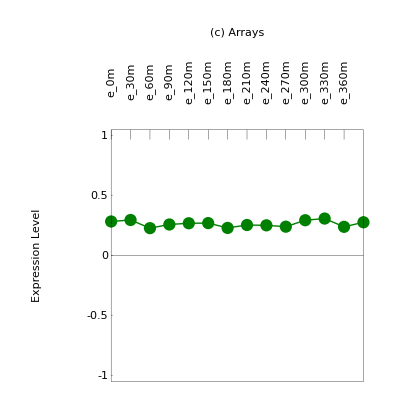

```mathematica
labelx=ColumnForm[{"(c) Arrays"},Center];
labely=ColumnForm[{" ","Expression Level"},Center];
framex=Table[{a-1,arraynames[[2,a]]},{a,1,arrays}];
framey={-1,-0.5,0,0.5,1};
coordinates=Table[{a-1,eigengenes[[1,a]]},	{a,1,arrays}];
points=Table[Point[coordinates[[a]]],	{a,1,arrays}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[0,0.5,0],PointSize[0.022],points}],
			Graphics[{RGBColor[0,0.5,0],line}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,{{0,RGBColor[0,0,0]}}},
	FrameTicks->{None,framey,framex,None},
	PlotRange->{-1.05,1.05},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3.6,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+0.6},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+0.24},{0,0},{0,1}];
p1=Show[g,
		AspectRatio->1.05,
		PlotRange->All]
```

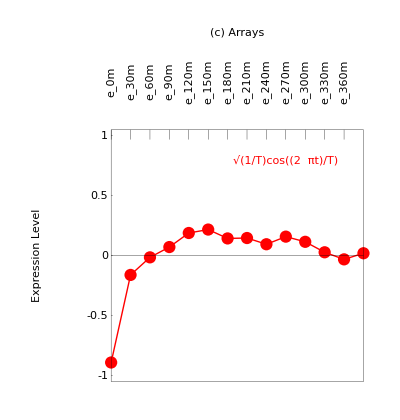

```mathematica
graph=Plot[
		eigengenes2,
		{x,0,arrays-1},
		PlotStyle->{RGBColor[1,0,0],Dashing[{0.03,0.02}]},
		DisplayFunction->Identity];
labelx=ColumnForm[{"(c) Arrays"},Center];
labely=ColumnForm[{" ","Expression Level"},Center];
framex=Table[{a-1,arraynames[[2,a]]},{a,1,arrays}];
framey={-1,-0.5,0,0.5,1};
coordinates=Table[{a-1,eigengenes[[2,a]]},	{a,1,arrays}];
points=Table[Point[coordinates[[a]]],	{a,1,arrays}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[1,0,0],PointSize[0.022],points}],
			Graphics[{RGBColor[1,0,0],line}],
			graph,
			Graphics[{RGBColor[1,0,0],Text["√(1/T)cos((2  πt)/T)",{9,0.8}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,{{0,RGBColor[0,0,0]}}},
	FrameTicks->{None,framey,framex,None},
	PlotRange->{-1.05,1.05},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3.6,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+0.6},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+0.24},{0,0},{0,1}];
p2=Show[g,
		AspectRatio->1.05,
		PlotRange->All]
```

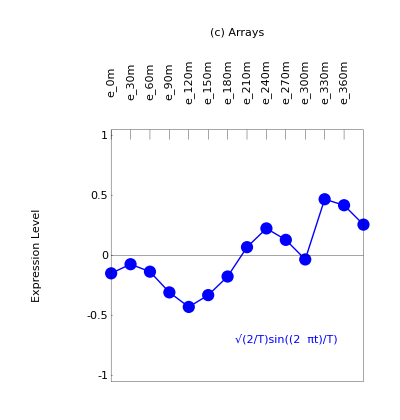

```mathematica
graph=Plot[
		eigengenes3,
		{x,0,arrays-1},
		PlotStyle->{RGBColor[0,0,1],Dashing[{0.03,0.02}]},
		DisplayFunction->Identity];
labelx=ColumnForm[{"(c) Arrays"},Center];
labely=ColumnForm[{" ","Expression Level"},Center];
framex=Table[{a-1,arraynames[[2,a]]},{a,1,arrays}];
framey={-1,-0.5,0,0.5,1};
coordinates=Table[{a-1,eigengenes[[3,a]]},	{a,1,arrays}];
points=Table[Point[coordinates[[a]]],	{a,1,arrays}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[0,0,1],PointSize[0.022],points}],
			Graphics[{RGBColor[0,0,1],line}],
			graph,
			Graphics[{RGBColor[0,0,1],Text["√(2/T)sin((2  πt)/T)",{9,-0.7}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,{{0,RGBColor[0,0,0]}}},
	FrameTicks->{None,framey,framex,None},
	PlotRange->{-1.05,1.05},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3.6,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+0.6},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+0.24},{0,0},{0,1}];
p3=Show[g,
		AspectRatio->1.05,
		PlotRange->All]
```

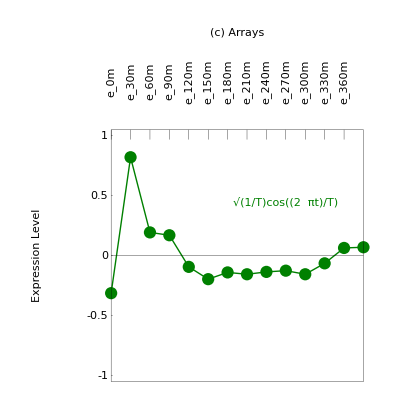

```mathematica
graph=Plot[
		eigengenes4,
		{x,0,arrays-1},
		PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.02}]},
		DisplayFunction->Identity];
labelx=ColumnForm[{"(c) Arrays"},Center];
labely=ColumnForm[{" ","Expression Level"},Center];
framex=Table[{a-1,arraynames[[2,a]]},{a,1,arrays}];
framey={-1,-0.5,0,0.5,1};
coordinates=Table[{a-1,eigengenes[[4,a]]},	{a,1,arrays}];
points=Table[Point[coordinates[[a]]],	{a,1,arrays}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[0,0.5,0],PointSize[0.022],points}],
			Graphics[{RGBColor[0,0.5,0],line}],
			graph,
			Graphics[{RGBColor[0,0.5,0],Text["√(1/T)cos((2  πt)/T)",{9,0.45}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,{{0,RGBColor[0,0,0]}}},
	FrameTicks->{None,framey,framex,None},
	PlotRange->{-1.05,1.05},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3.6,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+0.6},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+0.24},{0,0},{0,1}];
p4=Show[g,
		AspectRatio->1.05,
		PlotRange->All]
```

```mathematica
(* Display Selected Eigengenes *)
```

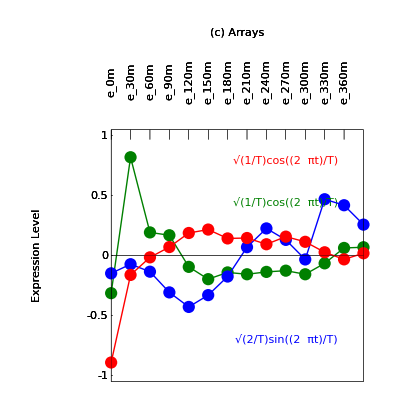

```mathematica
g3=Show[{p4,p3,p2},
		DisplayFunction->Identity]
```

```mathematica
(* Display Eigengenes, Fractions and Selected Eigengenes *)
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

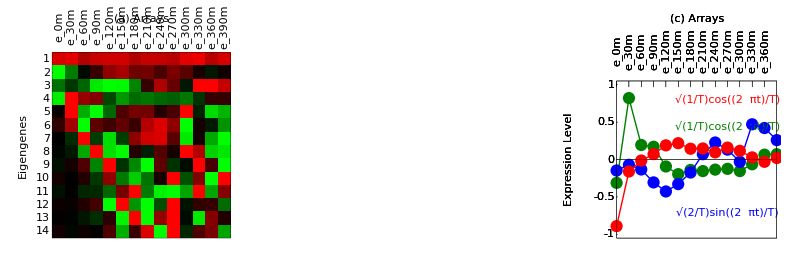

```mathematica
Show[GraphicsArray[{g1,g2,g3}],
	GraphicsSpacing->-0.125]
```

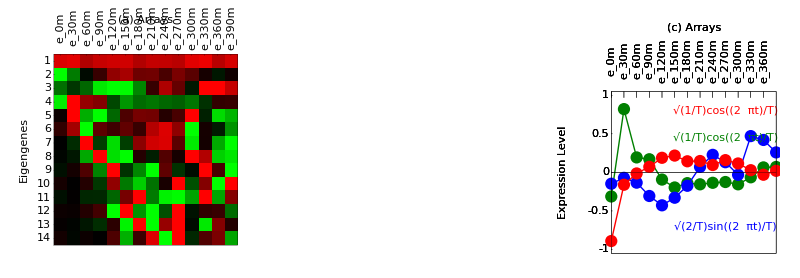

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.000629649, 0.000712763, 0.000834623, 0.00107096, 0.00122134, 0.0012675, 0.00152336, 0.00193597, 0.00273762, 0.00357581, 0.0064118, 0.0129389, 0.0311582, 0.933982}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity].

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.000629649, 0.000712763, 0.000834623, 0.00107096, 0.00122134, 0.0012675, 0.00152336, 0.00193597, 0.00273762, 0.00357581, 0.0064118, 0.0129389, 0.0311582}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity].

Show::gtype: FullGraphics is not a type of graphics.

Show::gcomb: Could not combine the graphics objects in « 1 ».

-Graphics-

```mathematica
(* and Remove the Additive Constant *)
```

```mathematica
(* Reconstruct Data Without Additive Constant *)
```

```mathematica
eigenexpressions[[1]]=0;
eigenexpressions
matrix=Dot[eigenarrays,DiagonalMatrix[eigenexpressions],eigengenes];
```

{0,49.3231,31.7843,22.3746,16.7091,14.6201,12.2946,10.906,9.94807,9.76523,9.14432,8.07253,7.45997,7.01155}

```mathematica
(* Remove the Multiplicative Constant *)
```

```mathematica
(* Calculate Singular Value Decomposition *)
```

```mathematica
normalization=Log[matrix^2];
correlation=Dot[Transpose[normalization],normalization]/(arrays-1);
{eigenexpressions,eigengenes}=Eigensystem[correlation];
eigenexpressions=Sqrt[(arrays-1)*eigenexpressions];
eigenexpressions
Clear[correlation];

eigengenes[[2]]=-eigengenes[[2]];
eigenarrays=Dot[eigengenes,Transpose[normalization]];
Do[
	eigenarrays[[a]]=eigenarrays[[a]]/eigenexpressions[[a]],
	{a,1,arrays}];
eigenarrays=Transpose[eigenarrays];
eigenarrays[[1]]
fractions=eigenexpressions^2/Sum[eigenexpressions[[a]]^2,{a,1,arrays}];
entropy=-N[Sum[fractions[[a]]*Log[fractions[[a]]],{a,1,arrays}]/Log[arrays]];
entropy=N[Round[100*entropy]/100]
```

{1423.86,206.849,187.648,180.783,171.934,166.926,165.737,163.207,162.078,158.595,154.955,150.608,149.392,146.867}

{0.0143747,-0.00506767,0.00729164,0.0143341,-0.00785769,-0.0114576,-0.0376682,0.0158961,-0.00689783,0.0154951,-0.0108624,-0.0165426,-0.00364507,0.00716521}

0.31

```mathematica
(* Create Fractions Bar Charts Displays *)
```

```mathematica
fractions[[2]]
```

0.0178904

```mathematica
limit=0.02;
```

```mathematica
Clear[gridx,framex,framey,sizes];
gridx=Table[a,{a,0,limit,N[limit/4]}];
framex=gridx;
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[framex[[a]]]
				]
			],{a,1,5}]];
Do[
	Do[framex[[a]]=StringJoin[ToString[framex[[a]]]," "],
	       {b,1,5-sizes[[a]]}],
    	{a,1,5}];
framex=Table[{gridx[[a]],framex[[a]]},{a,1,5}];
gridx=Table[{gridx[[a]],RGBColor[0,0,0]},{a,1,5}];
framey=Table[{a+1,arrays-a},{a,0,arrays-2}];
table=Table[fractions[[arrays-a]],{a,0,arrays-2}];
g=BarChart[
		table,
		BarOrientation->Horizontal,
		PlotRange->{{0,limit*1.0001},{0.5,arrays-1+0.5}},
		AspectRatio->1,
		Axes->False,
		Frame->True,
		FrameTicks->{None,framey,framex,None},
		FrameLabel->{None,None,None,None},		
		GridLines->{gridx,None},
		DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+2},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->1.25,
	PlotRange->All,
	DisplayFunction->Identity];
```

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.00901909, 0.00933184, 0.00948438, 0.0100397, 0.010517, 0.010984, 0.0111375, 0.0114856, 0.0116509, 0.0123605, 0.0136656, 0.0147232, 0.0178904}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity].

Show::gtype: FullGraphics is not a type of graphics.

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.00901909, 0.00933184, 0.00948438, 0.0100397, 0.010517, 0.010984, 0.0111375, 0.0114856, 0.0116509, 0.0123605, 0.0136656, 0.0147232, 0.0178904, 0.84771}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity].

Show::gcomb: Could not combine the graphics objects in {FullGraphics[BarChart[{0.009019087278899938`, 0.009331842740657655`, 0.009484383579538866`, 0.010039743793421462`, 0.010516987975144639`, 0.010984008332142753`, 0.011137541760661672`, 0.011485579899052703`, 0.011650914887102825`, 0.012360471969146592`, 0.013665550204467136`, 0.014723213419898518`, 0.017890430243083594`, 0.8477102439167814`}, BarOrientation → Horizontal, « 7 », DisplayFunction → Identity]], GraphicsBox[List[RGBColor[1, 1, 0.8`], RectangleBox[List[0.1`, 0.6`], List[0.98`, 13]]]], GraphicsBox[List[InsetBox[BoxData[FormBox[RowBox[List[.

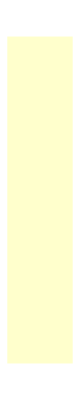
Show[{FullGraphics[BarChart[{0.00901909,0.00933184,0.00948438,0.0100397,0.010517,0.010984,0.0111375,0.0114856,0.0116509,0.0123605,0.0136656,0.0147232,0.0178904,0.84771},BarOrientation→Horizontal,PlotRange→{{0,1.0001},{0.5,14.5}},AspectRatio→1,Axes→False,Frame→True,FrameTicks→{None,{{1,14},{2,13},{3,12},{4,11},{5,10},{6,9},{7,8},{8,7},{9,6},{10,5},{11,4},{12,3},{13,2},{14,1}},{{0.,0.    },{0.2,0.2   },{0.4,0.4   },{0.6,0.6   },{0.8,0.8   },{1.,1.    }},None},FrameLabel→{None,None,(b) Eigenexpression Fraction
d = 0.31
 ,None},GridLines→{{{0.,RGBColor[0,0,0]},{0.2,RGBColor[0,0,0]},{0.4,RGBColor[0,0,0]},{0.6,RGBColor[0,0,0]},{0.8,RGBColor[0,0,0]},{1.,RGBColor[0,0,0]}},None},DisplayFunction→Identity]],-Graphics-,-Graphics-},AspectRatio→1.35,PlotRange→All,DisplayFunction→Identity]

```mathematica
gridx=Table[a,{a,0,1,0.2}];
framex=gridx;
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[framex[[a]]]
				]
			],{a,1,6}]];
Do[
	Do[framex[[a]]=StringJoin[ToString[framex[[a]]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,6}];
framex=Table[{gridx[[a]],
			framex[[a]]},{a,1,6}];
gridx=Table[{gridx[[a]],RGBColor[0,0,0]},{a,1,6}];
framey=Table[{a+1,arrays-a},{a,0,arrays-1}];
labelx=ColumnForm[
		{"(b) Eigenexpression Fraction",StringJoin["d = ",ToString[entropy]]," "},Center];
g=BarChart[
		Table[fractions[[arrays-a]],{a,0,arrays-1}],
		BarOrientation->Horizontal,
		PlotRange->{{0,1.0001},{0.5,arrays+0.5}},
		AspectRatio->1,
		Axes->False,
		Frame->True,
		FrameTicks->{None,framey,framex,None},
		FrameLabel->{None,None,labelx,None},
		GridLines->{gridx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.8},{0,0},{0,1}];
g2=Show[{g,
			Graphics[{RGBColor[1,1,0.8],Rectangle[{0.1,0.6},{0.98,13}]}],
			Graphics[{Rectangle[{0.1,0.6},{0.98,13},g1]}]},
	AspectRatio->1.35,
	PlotRange->All,
	DisplayFunction->Identity]
```

```mathematica
(* Create Eigengenes 2D Red & Green Raster Display *)
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

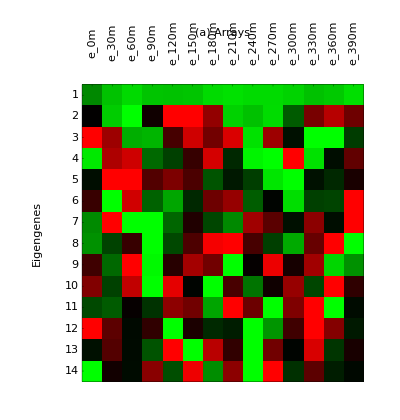

```mathematica
contrast=3;
displaying=Table[
		If[contrast*eigengenes[[i,j]]>0,
			If[contrast*eigengenes[[i,j]]<1,{contrast*eigengenes[[i,j]],0},{1,0}],
			If[contrast*eigengenes[[i,j]]>-1,{0,-contrast*eigengenes[[i,j]]},{0,1}]],
		{i,1,arrays},{j,1,arrays}];
framex=Table[{a-0.5,arraynames[[2,a]]},{a,1,arrays}];
framey=Table[{a+1-0.5,arrays-a},{a,0,arrays-1}];
labely="Eigengenes";
labelx=ColumnForm[{"(a) Arrays"," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,arrays,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-2,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.8},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->1.05,
	PlotRange->All,
	DisplayFunction->Identity]
```

```mathematica
(* Display Both Eigengenes & Fractions *)
```

```mathematica
Show[GraphicsArray[{g1,g2}],
	GraphicsSpacing->-0.125]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
(* Reconstruct the Data Without Multiplicative Constant *)
```

```mathematica
eigenexpressions[[1]]=0;
normalization=Dot[eigenarrays,DiagonalMatrix[eigenexpressions],eigengenes];
normalization[[1]]
Exp[normalization][[1]]
normalization=Sqrt[Exp[normalization]];
normalization[[1]]
matrix[[1]]
matrix=Sign[matrix];
matrix[[1]]
matrix=N[matrix*normalization];
matrix[[1]]
Clear[normalization];
```

{-0.726456,-1.76207,2.34809,0.98007,1.4926,0.203397,0.302207,2.93059,-1.66168,0.150234,2.36505,-4.60147,2.29901,-4.76621}

{0.48362,0.171689,10.4656,2.66464,4.44865,1.22556,1.35284,18.7387,0.18982,1.16211,10.6445,0.0100371,9.9643,0.00851254}

{0.695428,0.414354,3.23505,1.63237,2.10918,1.10705,1.16312,4.32882,0.435683,1.07801,3.26259,0.100185,3.15663,0.0922635}

{0.112372,-0.0310689,0.174335,0.118744,-0.156684,0.0790179,-0.0618006,0.213784,0.0233057,-0.057883,-0.193946,0.00753201,-0.213674,0.0046992}

{1,-1,1,1,-1,1,-1,1,1,-1,-1,1,-1,1}

{0.695428,-0.414354,3.23505,1.63237,-2.10918,1.10705,-1.16312,4.32882,0.435683,-1.07801,-3.26259,0.100185,-3.15663,0.0922635}

```mathematica
(* Examine Normalized Data *)
```

```mathematica
(* Calculate Singular Value Decomposition *)
```

```mathematica
correlation=Dot[Transpose[matrix],matrix]/(arrays-1);
correlation[[1]]
{eigenexpressions,eigengenes}=Eigensystem[correlation];
eigenexpressions=Sqrt[(arrays-1)*eigenexpressions];
Clear[correlation];
eigengenes[[1]]=-eigengenes[[1]];
eigenarrays=Dot[eigengenes,Transpose[matrix]];
Do[
	eigenarrays[[a]]=eigenarrays[[a]]/eigenexpressions[[a]],
	{a,1,arrays}];
eigenarrays=Transpose[eigenarrays];
arraycorrelations=Dot[DiagonalMatrix[eigenexpressions],eigengenes];
genecorrelations=Dot[eigenarrays,DiagonalMatrix[eigenexpressions]];
genecorrelations=Transpose[genecorrelations];
fractions=eigenexpressions^2/Sum[eigenexpressions[[a]]^2,{a,1,arrays}];
entropy=-N[Sum[fractions[[a]]*Log[fractions[[a]]],{a,1,arrays}]/Log[arrays]];
entropy=N[Round[100*entropy]/100]
```

{1774.87,226.138,71.3927,-275.547,-565.525,-718.347,-548.564,-696.235,-434.985,-841.06,-320.141,-182.908,-11.8498,-244.445}

0.88

```mathematica
(* Create Fractions Bar Charts Displays *)
```

```mathematica
fractions[[1]]
```

0.22391

```mathematica
limit=0.25;
```

```mathematica
Clear[gridx,framex,framey,sizes];
gridx=Table[a,{a,0,limit,N[limit/5]}];
framex=gridx;
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[framex[[a]]]
				]
			],{a,1,6}]];
Do[
	Do[framex[[a]]=StringJoin[ToString[framex[[a]]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,6}];
framex=Table[{gridx[[a]],framex[[a]]},{a,1,6}];
framey=Table[{a+1,arrays-a},{a,0,arrays-1}];
labelx=ColumnForm[
		{"(b) Eigenexpression Fraction",StringJoin["d = ",ToString[entropy]]," "},Center];
g=BarChart[
		Table[fractions[[arrays-a]],{a,0,arrays-1}],
		BarOrientation->Horizontal,
		PlotRange->{{0,limit*1.0001},{0.5,arrays+0.5}},
		AspectRatio->1,
		Axes->False,
		Frame->True,
		FrameTicks->{None,framey,framex,None},
		FrameLabel->{None,None,labelx,None},		
		GridLines->{gridx,None},
		DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.8},{0,0},{0,1}];
g2=Show[g,
	AspectRatio->1.35,
	PlotRange->All,
	DisplayFunction->Identity];
```

BarChart::optx: Unknown option BarOrientation → Horizontal in BarChart[{0.00104535, 0.0264764, 0.0304115, 0.0349395, 0.0417187, 0.0426261, 0.0452534, 0.0528704, 0.0616225, 0.0706758, 0.0842651, 0.0887297, 0.195456, 0.22391}, BarOrientation → Horizontal, « 6 », GridLines → {{0., 0.05, 0.1, 0.15, 0.2, 0.25}, None}, DisplayFunction → Identity].

Show::gtype: FullGraphics is not a type of graphics.

```mathematica
(* Create Eigengenes 2D Red & Green Raster Display *)
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

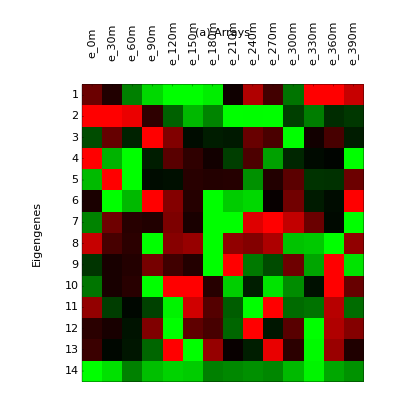

```mathematica
contrast=3;
displaying=Table[
		If[contrast*eigengenes[[i,j]]>0,
			If[contrast*eigengenes[[i,j]]<1,{contrast*eigengenes[[i,j]],0},{1,0}],
			If[contrast*eigengenes[[i,j]]>-1,{0,-contrast*eigengenes[[i,j]]},{0,1}]],
		{i,1,arrays},{j,1,arrays}];
framex=Table[{a-0.5,arraynames[[2,a]]},{a,1,arrays}];
framey=Table[{a+1-0.5,arrays-a},{a,0,arrays-1}];
labely="Eigengenes";
labelx=ColumnForm[{"(a) Arrays"," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,arrays,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-2,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+1.8},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->1.05,
	PlotRange->All,
	DisplayFunction->Identity]
```

```mathematica
(* Create Selected Eigengenes Graph Display *)
```

```mathematica
eigengenes1=Chop[TrigFit[eigengenes[[1]],2,{x,arrays-1}],0.12]
eigengenes2=Chop[TrigFit[eigengenes[[2]],2,{x,arrays-1}],0.1]
```

TrigFit[{0.14033,0,-0.1679,-0.283551,-0.431031,-0.378029,-0.311194,0,0.230281,0,-0.152281,0.391211,0.374125,0.259599},2,{x,13}]

TrigFit[{0.44652,0.38108,0.307462,0,-0.127263,-0.240726,-0.172174,-0.3744,-0.332151,-0.401101,0,-0.163371,0,0},2,{x,13}]

```mathematica
eigengenes1=0.39*Sin[2*Pi*(x-1)/13];
eigengenes2=0.39*Cos[2*Pi*(x-1)/13];
```

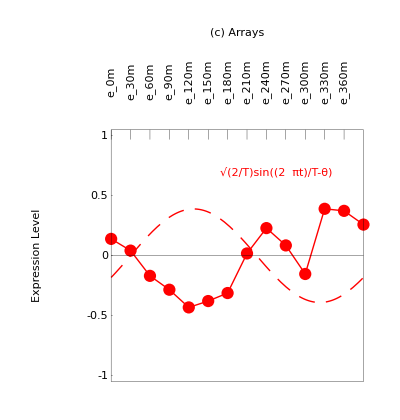

```mathematica
graph=Plot[
		eigengenes1,
		{x,0,arrays-1},
		PlotStyle->{RGBColor[1,0,0],Dashing[{0.03,0.02}]},
		DisplayFunction->Identity];
labelx=ColumnForm[{"(c) Arrays"},Center];
labely=ColumnForm[{" ","Expression Level"},Center];
framex=Table[{a-1,arraynames[[2,a]]},{a,1,arrays}];
framey={-1,-0.5,0,0.5,1};
coordinates=Table[{a-1,eigengenes[[1,a]]},	{a,1,arrays}];
points=Table[Point[coordinates[[a]]],	{a,1,arrays}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[1,0,0],PointSize[0.022],points}],
			Graphics[{RGBColor[1,0,0],line}],
			graph,
			Graphics[{RGBColor[1,0,0],Text["√(2/T)sin((2  πt)/T-θ)",{8.5,0.7}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,{{0,RGBColor[0,0,0]}}},
	FrameTicks->{None,framey,framex,None},
	PlotRange->{-1.05,1.05},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3.6,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+0.6},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+0.24},{0,0},{0,1}];
p1=Show[g,
		AspectRatio->1.05,
		PlotRange->All]
```

```mathematica
graph=Plot[
		eigengenes2,
		{x,0,arrays-1},
		PlotStyle->{RGBColor[0,0,1],Dashing[{0.03,0.02}]},
		DisplayFunction->Identity];
labelx=ColumnForm[{"(c) Arrays"},Center];
labely=ColumnForm[{" ","Expression Level"},Center];
framex=Table[{a-1,arraynames[[2,a]]},{a,1,arrays}];
framey={-1,-0.5,0,0.5,1};
coordinates=Table[{a-1,eigengenes[[2,a]]},	{a,1,arrays}];
points=Table[Point[coordinates[[a]]],	{a,1,arrays}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[0,0,1],PointSize[0.022],points}],
			Graphics[{RGBColor[0,0,1],line}],
			graph,
			Graphics[{RGBColor[0,0,1],Text["√(2/T)cos((2  πt)/T-θ)",{8.5,-0.7}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,{{0,RGBColor[0,0,0]}}},
	FrameTicks->{None,framey,framex,None},
	PlotRange->{-1.05,1.05},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3.6,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+0.6},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+0.24},{0,0},{0,1}];
p2=Show[g,
		AspectRatio->1.05,
		PlotRange->All];
```

```mathematica
(* Display Selected Eigengenes *)
```

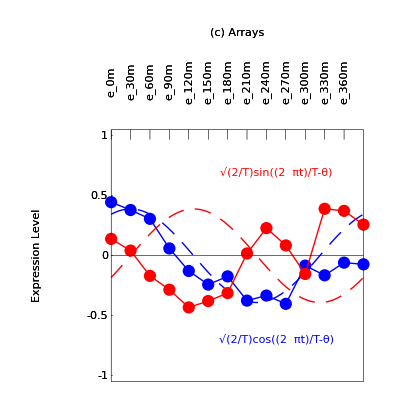

```mathematica
g3=Show[{p2,p1},
	DisplayFunction->Identity]
```

```mathematica
(* Display Eigengenes, Fractions and Selected Eigengenes *)
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

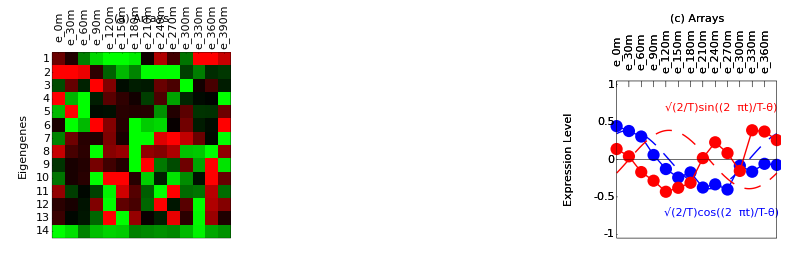

```mathematica
Show[GraphicsArray[{g1,g2,g3}],
	GraphicsSpacing->-0.125]
```

```mathematica
(* Create Parameter Graphs of Arrays According to Projections on Eigenarrays *)
```

```mathematica
labelx=ColumnForm[{"Array Correlation with |α_2⟩"},Center];
labely=ColumnForm[{"Array Correlation with |α_1⟩"},Center];
matrix=Transpose[matrix];
coordinates=Table[
		{arraycorrelations[[2,a]]/Sqrt[Dot[matrix[[a]],matrix[[a]]]],
			arraycorrelations[[1,a]]/Sqrt[Dot[matrix[[a]],matrix[[a]]]]},
		{a,1,arrays}];
matrix=Transpose[matrix];
points1={Point[coordinates[[1]]],Point[coordinates[[2]]],Point[coordinates[[14]]]};
points2=Table[Point[coordinates[[a]]],{a,3,6}];
points3=Table[Point[coordinates[[a]]],{a,7,8}];
points4=Table[Point[coordinates[[a]]],{a,9,10}];
points5=Table[Point[coordinates[[a]]],{a,11,13}];
textcoordinates=coordinates;
Do[textcoordinates[[a,1]]=
		If[textcoordinates[[a,1]]>0,textcoordinates[[a,1]]+0.085,textcoordinates[[a,1]]-0.085],
	{a,1,9}];
Do[textcoordinates[[a,1]]=
		If[textcoordinates[[a,1]]>0,textcoordinates[[a,1]]+0.11,textcoordinates[[a,1]]-0.11],
	{a,10,arrays}];
textcoordinates[[4]]=textcoordinates[[4]]+{0,0.02};
textcoordinates[[8]]=textcoordinates[[8]]+{0,-0.02};
textcoordinates[[13]]=textcoordinates[[13]]+{0.01,0.04};
textcoordinates[[14]]=textcoordinates[[14]]+{0.085,0.085};
texts=Table[Text[a,textcoordinates[[a]]],{a,1,arrays}];
zerophase=N[ArcTan[arraycorrelations[[1,1]]/arraycorrelations[[2,1]]]];
```

```mathematica
p=Show[{
		Graphics[{RGBColor[1,1,0],PointSize[0.035],points1}],
		Graphics[{RGBColor[0,0.5,0],PointSize[0.035],points2}],
		Graphics[{RGBColor[0,0,1],PointSize[0.035],points3}],
		Graphics[{RGBColor[1,0,0],PointSize[0.035],points4}],
		Graphics[{RGBColor[1,0.5,0],PointSize[0.035],points5}],
		Graphics[{RGBColor[1,0.5,0],Text["G2/M",{-0.6,-0.95}]}],
		Graphics[{RGBColor[0,0,0],Text["M/G1",{0.8,-0.85}]}],
		Graphics[{RGBColor[1,0,0],Text["S/G2",{-0.875,-0.75}]}],
		Graphics[{RGBColor[0,0,1],Text["S",{-0.95,0.5}]}],
		Graphics[{RGBColor[0,0.5,0],Text["G1",{0.55,0.95}]}],
		Graphics[{RGBColor[0,0,0],Text["(a)",{-0.9,0.95}]}],
		Graphics[texts],
		Graphics[{RGBColor[0,0,0],Dashing[{0.03,0.02}],Circle[{0,0},1]}],
		Graphics[{RGBColor[0,0,0],Dashing[{0.03,0.02}],Circle[{0,0},0.5]}],
		Graphics[{RGBColor[0,0,0],Circle[{0,0},0.45,{zerophase,0}]}],
		Graphics[{RGBColor[0,0,0],Arrow[
					{0.45*Cos[-0.05],0.45*Sin[-0.05]},{0.45*Cos[0],0.45*Sin[0]},
					HeadCenter->0.5,HeadLength->0.035,HeadWidth->0.75]}],
		Graphics[{RGBColor[0,0,0],Circle[{0,0},0.9,{zerophase,-2*zerophase}]}],
		Graphics[{RGBColor[0,0,0],Arrow[
						{0.9*Cos[-2*zerophase-0.05],0.9*Sin[-2*zerophase-0.05]},
						{0.9*Cos[-2*zerophase],0.9*Sin[-2*zerophase]},
						HeadCenter->0.5,HeadLength->0.035,HeadWidth->0.75]}],
		Graphics[{RGBColor[0,0,0],Arrow[{0,0},coordinates[[1]],
						HeadCenter->0.5,HeadLength->0.035,HeadWidth->0.75]}],
		Graphics[{RGBColor[0,0,0],Text["r",{0.65,-0.35}]}],
		Graphics[{RGBColor[0,0,0],Text["θ",{0.35,-0.05}]}]},
	AspectRatio->1,
	PlotRange->{{-1.05,1.05},{-1.05,1.05}},
	Frame->True,
	FrameTicks->False,
	FrameLabel->{labelx,labely,None,None},
	GridLines->{{{0,RGBColor[0,0,0]}},{{0,RGBColor[0,0,0]}}},
	DisplayFunction->Identity];
p=FullGraphics[p];
p[[1,2]]=p[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{-1.18,0},{0,0},{0,1}];
p1=Show[p,
	AspectRatio->1.,
	PlotRange->All,
	DisplayFunction->Identity]
```

-Graphics-

```mathematica
(* Create Parameter Graphs of Genes According to Projections on Eigengenes *)
```

```mathematica
labelx=ColumnForm[{"Gene Correlation with |γ_2⟩"},Center];
labely=ColumnForm[{"Gene Correlation with |γ_1⟩"},Center];
coordinates=Table[
		{genecorrelations[[2,a]]/Sqrt[Dot[matrix[[a]],matrix[[a]]]],
			genecorrelations[[1,a]]/Sqrt[Dot[matrix[[a]],matrix[[a]]]]},
		{a,1,genes}];
points=Table[Point[coordinates[[a]]],	{a,1,genes}];
stream=StringJoin[name,":Desktop Folder:PNAS Data:Classify_Elutriation.txt"];list=ReadList[stream,Word,RecordLists->True,NullWords->True];
list=Drop[list,2];
```

StringJoin::string: String expected at position 1 in name <> ":Desktop Folder:PNAS Data:Classify_Elutriation.txt".

General::stream: name <> ":Desktop Folder:PNAS Data:Classify_Elutriation.txt" is not a string, InputStream[ ], or OutputStream[ ].

General::openx: name <> ":Desktop Folder:PNAS Data:Classify_Elutriation.txt" is not open.

ReadList::nffil: File not found during ReadList[name <> ":Desktop Folder:PNAS Data:Classify_Elutriation.txt", Word, RecordLists → True, NullWords → True].

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, 2].

```mathematica
position=Position[list,"M/G1"];
points1=Table[Point[coordinates[[position[[a,1]]]]],{a,1,Dimensions[position][[1]]}];
radii1=Table[Sqrt[coordinates[[position[[a,1]],1]]^2+coordinates[[position[[a,1]],2]]^2],
			{a,1,Dimensions[position][[1]]}];
Dimensions[points1][[1]]
position=Position[list,"G1"];
points2=Table[Point[coordinates[[position[[a,1]]]]],{a,1,Dimensions[position][[1]]}];
radii2=Table[Sqrt[coordinates[[position[[a,1]],1]]^2+coordinates[[position[[a,1]],2]]^2],
			{a,1,Dimensions[position][[1]]}];
Dimensions[points2][[1]]
position=Position[list,"S"];
points3=Table[Point[coordinates[[position[[a,1]]]]],{a,1,Dimensions[position][[1]]}];
radii3=Table[Sqrt[coordinates[[position[[a,1]],1]]^2+coordinates[[position[[a,1]],2]]^2],
			{a,1,Dimensions[position][[1]]}];
Dimensions[points3][[1]]
position=Position[list,"S/G2"];
points4=Table[Point[coordinates[[position[[a,1]]]]],{a,1,Dimensions[position][[1]]}];
radii4=Table[Sqrt[coordinates[[position[[a,1]],1]]^2+coordinates[[position[[a,1]],2]]^2],
			{a,1,Dimensions[position][[1]]}];
Dimensions[points4][[1]]
position=Position[list,"G2/M"];
points5=Table[Point[coordinates[[position[[a,1]]]]],{a,1,Dimensions[position][[1]]}];
radii5=Table[Sqrt[coordinates[[position[[a,1]],1]]^2+coordinates[[position[[a,1]],2]]^2],
			{a,1,Dimensions[position][[1]]}];
Dimensions[points5][[1]]
```

0

0

0

«2 more identical outputs»

```mathematica
radii=AppendRows[{radii1},{radii2},{radii3},{radii4},{radii5}][[1]];
radii=Sort[radii, OrderedQ[{{#1}, {#2}}]&];
N[Round[radii[[143]]*100]/100]
N[Round[radii[[144]]*100]/100]
```

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

Part::partw: Part 143 of {} does not exist.

0.01 Round[100. {}⟦143⟧]

Part::partw: Part 144 of {} does not exist.

0.01 Round[100. {}⟦144⟧]

```mathematica
(* 784 cell cycle genes, 112 in M/G1, 295 in G1, 69 in S, 116 in S/G2, 192 in G2/M. *)
```

```mathematica
(* 641 with more than 25% of normalized expression in the cell cycle subspace. *)
```

```mathematica
p=Show[{
		Graphics[{RGBColor[0,0,0],PointSize[0.01],points}],
		Graphics[{RGBColor[1,0.5,0],Text["G2/M",{-0.6,-0.95}]}],
		Graphics[{RGBColor[0,0,0],Text["M/G1",{0.8,-0.85}]}],
		Graphics[{RGBColor[1,0,0],Text["S/G2",{-0.875,-0.75}]}],
		Graphics[{RGBColor[0,0,1],Text["S",{-0.95,0.5}]}],
		Graphics[{RGBColor[0,0.5,0],Text["G1",{0.55,0.95}]}],
		Graphics[{RGBColor[0,0,0],Text["(b)",{-0.9,0.95}]}],
		Graphics[{RGBColor[0,0,0],Dashing[{0.03,0.02}],Circle[{0,0},1]}]},
	AspectRatio->1,
	PlotRange->{{-1.05,1.05},{-1.05,1.05}},
	Frame->True,
	FrameTicks->False,
	FrameLabel->{labelx,labely,None,None},
	GridLines->{{{0,RGBColor[0,0,0]}},{{0,RGBColor[0,0,0]}}},
	DisplayFunction->Identity];
```

```mathematica
p=FullGraphics[p];
p[[1,2]]=p[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{-1.18,0},{0,0},{0,1}];
p2=Show[p,
	AspectRatio->1.,
	PlotRange->All,
	DisplayFunction->Identity];
```

```mathematica
p=Show[{
		Graphics[{RGBColor[1,0.5,0],PointSize[0.02],points5}],
		Graphics[{RGBColor[1,1,0],PointSize[0.02],points1}],
		Graphics[{RGBColor[1,0,0],PointSize[0.02],points4}],
		Graphics[{RGBColor[0,0.5,0],PointSize[0.02],points2}],
		Graphics[{RGBColor[0,0,1],PointSize[0.02],points3}],
		Graphics[{RGBColor[1,0.5,0],Text["G2/M",{-0.6,-0.95}]}],
		Graphics[{RGBColor[0,0,0],Text["M/G1",{0.8,-0.85}]}],
		Graphics[{RGBColor[1,0,0],Text["S/G2",{-0.875,-0.75}]}],
		Graphics[{RGBColor[0,0,1],Text["S",{-0.95,0.5}]}],
		Graphics[{RGBColor[0,0.5,0],Text["G1",{0.55,0.95}]}],
		Graphics[{RGBColor[0,0,0],Text["(c)",{-0.9,0.95}]}],
		Graphics[{RGBColor[0,0,0],Dashing[{0.03,0.02}],Circle[{0,0},1]}],
		Graphics[{RGBColor[0,0,0],Dashing[{0.03,0.02}],Circle[{0,0},0.5]}]},
	AspectRatio->1,
	PlotRange->{{-1.05,1.05},{-1.05,1.05}},
	Frame->True,
	FrameTicks->False,
	FrameLabel->{labelx,labely,None,None},
	GridLines->{{{0,RGBColor[0,0,0]}},{{0,RGBColor[0,0,0]}}},
	DisplayFunction->Identity];
p=FullGraphics[p];
p[[1,2]]=p[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{-1.18,0},{0,0},{0,1}];
p3=Show[p,
	AspectRatio->1.,
	PlotRange->All,
	DisplayFunction->Identity];
```

```mathematica
(* Display Both Arrays & Genes Parameter Graphs *)
```

```mathematica
Show[GraphicsArray[{p1,p2,p3}],
	GraphicsSpacing->0]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
(* Sort Normalized Data *)
```

```mathematica
(* Define the Initial Phase According to the Initial Array *)
```

```mathematica
zerophase=N[ArcTan[arraycorrelations[[1,1]]/arraycorrelations[[2,1]]]/Pi]
```

0.103286

```mathematica
(* Sort Data by Phase *)
```

```mathematica
radii=Table[Sqrt[coordinates[[a,1]]^2+coordinates[[a,2]]^2],{a,1,genes}];
coordinates=Table[
		{genecorrelations[[2,a]]/Sqrt[genecorrelations[[1,a]]^2+genecorrelations[[2,a]]^2],
			genecorrelations[[1,a]]/Sqrt[genecorrelations[[1,a]]^2+genecorrelations[[2,a]]^2],
			N[ArcTan[genecorrelations[[1,a]]/genecorrelations[[2,a]]]/Pi],
			radii[[a]]},
		{a,1,genes}];
sortmatrix=AppendRows[coordinates,genenames,matrix];
sortmatrix=Sort[sortmatrix, OrderedQ[{{#1}, {#2}}]&];
negative1=3106;
positive1=3107;
sortmatrix[[negative1,1]]
sortmatrix[[positive1,1]]
```

-0.00016311

0.000620348

```mathematica
sortmatrix=Transpose[Drop[Transpose[sortmatrix],{1}]];
sortmatrix=AppendColumns[
		Sort[
			TakeRows[sortmatrix,{1,negative1}],
			 OrderedQ[{{#2}, {#1}}]&],
		Sort[
			TakeRows[sortmatrix,{positive1,genes}],
			 OrderedQ[{{#1}, {#2}}]&]
		];
sortmatrix=Transpose[Drop[Transpose[sortmatrix],{1}]];
```

```mathematica
(* Correct for the Phase & Calibrate According to the Initial Phase *)
```

```mathematica
Do[sortmatrix[[a,1]]=sortmatrix[[a,1]]-zerophase,
	{a,1,negative1}];
Do[sortmatrix[[a,1]]=sortmatrix[[a,1]]+1-zerophase,
	{a,positive1,genes}];
negative2=1322;
positive2=1323;
sortmatrix[[negative2,1]]
sortmatrix[[positive2,1]]
```

-0.174904

-0.174267

```mathematica
sortmatrix=AppendColumns[
		TakeRows[sortmatrix,{positive2,genes}],
		TakeRows[sortmatrix,{1,negative2}]
		];
positive3=4659;
negative3=4660;
sortmatrix[[positive3,1]]
sortmatrix[[negative3,1]]
```

1.39618

-0.603235

```mathematica
Do[sortmatrix[[a,1]]=sortmatrix[[a,1]]+2,
	{a,negative3,genes}];
```

```mathematica
(* Reconstruct Data With Sorted Genes *)
```

```mathematica
matrix=TakeColumns[sortmatrix,{4,arrays+3}];
eigenarrays=Dot[eigengenes,Transpose[matrix]];
Do[
	eigenarrays[[a]]=eigenarrays[[a]]/eigenexpressions[[a]],
	{a,1,arrays}];
eigenarrays=Transpose[eigenarrays];
arraycorrelations=Dot[DiagonalMatrix[eigenexpressions],eigengenes];
genecorrelations=Dot[eigenarrays,DiagonalMatrix[eigenexpressions]];
genecorrelations=Transpose[genecorrelations];
```

```mathematica
(* Classify Gene Phases into Cell Cycle Phases *)
```

```mathematica
phases=TakeColumns[sortmatrix,{1,1}];
ph1=-zerophase;
ph2=0.5-zerophase;
ph3=1-zerophase;
ph4=1.25-zerophase;
ph5=1.5-zerophase;
```

```mathematica
endph5=260;
beginph1=261;
phases[[endph5]]-ph1
phases[[beginph1]]-ph1
```

{0.0213007}

{0.0219321}

```mathematica
endph1=1784;
beginph2=1785;
phases[[endph1]]-ph2
phases[[beginph2]]-ph2
```

{-0.00088155}

{0.000197463}

```mathematica
endph2=3128;
beginph3=3129;
phases[[endph2]]-ph3
phases[[beginph3]]-ph3
```

{-0.0797636}

{-0.0792709}

```mathematica
endph3=3816;
beginph4=3817;
phases[[endph3]]-ph4
phases[[beginph4]]-ph4
```

{-0.0649407}

{-0.0648466}

```mathematica
endph4=4659;
beginph5=4660;
phases[[endph4]]-ph5
phases[[beginph5]]-ph5
```

{-0.000528725}

{0.0000519195}

```mathematica
(* 5891 yeast genes, 1582 in M/G1, 1524 in G1, 1344 in S, 688 in S/G2, 843 in G2/M. *)
```

```mathematica
(* Create Classified Sorted Data 2D Red & Green Raster Display *)
```

```mathematica
contrast=2;
displaying=Table[
		If[contrast*matrix[[i,j]]>0,
			If[contrast*matrix[[i,j]]<1,{contrast*matrix[[i,j]],0},{1,0}],
			If[contrast*matrix[[i,j]]>-1,{0,-contrast*matrix[[i,j]]},{0,1}]],
		{i,1,genes},{j,1,arrays}];
framex=Table[{a-0.5,arraynames[[2,a]]},{a,1,arrays}];
framey={
	{genes-endph5/2,"M/G1"},
	{genes-(endph5+endph1)/2,"G1"},
	{genes-(endph1+endph2)/2,"S"},
	{genes-(endph2+endph3)/2,"S/G2"},
	{genes-(endph3+endph4)/2,"G2/M"},
	{(genes-endph4)/2,"M/G1"}};
gridy={
		{genes-endph1+0.5,{RGBColor[0,0,0]}},
		{genes-endph2+0.5,{RGBColor[0,0,0]}},
		{genes-endph3+0.5,{RGBColor[0,0,0]}},
		{genes-endph4+0.5,{RGBColor[0,0,0]}},
		{genes-endph5+0.5,{RGBColor[0,0,0]}}};
labelx="(a) Arrays";
labely=ColumnForm[{" ","Genes"," "," "," "," "," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,genes,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,
	Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,gridy},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{1.,0.}]->
			Text[a,{b-1,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+1000},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+450},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->GoldenRatio*1.15,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Create Classified Sorted Eigenarrays 2D Red & Green Raster Display *)
```

```mathematica
contrast=50;
displaying=Table[
		If[contrast*eigenarrays[[i,j]]>0,
			If[contrast*eigenarrays[[i,j]]<1,{contrast*eigenarrays[[i,j]],0},{1,0}],
			If[contrast*eigenarrays[[i,j]]>-1,{0,-contrast*eigenarrays[[i,j]]},{0,1}]],
		{i,1,genes},{j,1,arrays}];
labelx="(b) Eigenarrays";
labely=ColumnForm[{" "," "," "," "," "," "," "," "},Center];
framex=Table[{a-0.5,ToString[a]},{a,1,arrays}];
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					framex[[a,2]]
				]
			],{a,1,arrays}]];
Do[
	Do[framex[[a,2]]=StringJoin[framex[[a,2]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,arrays}];
framey={
	{genes-endph5/2,"    ",0},
	{genes-(endph5+endph1)/2,"  ",0},
	{genes-(endph1+endph2)/2," ",0},
	{genes-(endph2+endph3)/2,"    ",0},
	{genes-(endph3+endph4)/2,"    ",0},
	{(genes-endph4)/2,"    ",0}};
gridy={
		{genes-endph1+0.5,{RGBColor[0,0,0]}},
		{genes-endph2+0.5,{RGBColor[0,0,0]}},
		{genes-endph3+0.5,{RGBColor[0,0,0]}},
		{genes-endph4+0.5,{RGBColor[0,0,0]}},
		{genes-endph5+0.5,{RGBColor[0,0,0]}}};
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,genes,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,
	Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	GridLines->{None,gridy},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{1.,0.}]->
			Text[a,{b-1,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+1000},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+450},{0,0},{0,1}];
g2=Show[g,
	AspectRatio->GoldenRatio*1.15,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Create Classified Selected Eigenarrays Graph Display *)
```

```mathematica
eigenarrays=Transpose[eigenarrays];
```

```mathematica
eigenarrays1=Chop[TrigFit[eigenarrays[[1]],1,{x,genes-1}],0.0025]
eigenarrays2=Chop[TrigFit[eigenarrays[[2]],1,{x,genes-1}],0.0025]
```

TrigFit[{0.00299377,0.00425468,0.00419877,0.00522356,0.00408362,0,0.00279959,0.00362331,0.00436888,0.00320416,0.0062007,0.00418622,«5957»,0.00498342,0.00488404,0,0,0.00568514,0.00256107,0.00262465,0.00471397,0,0.00577577,0.00322888,0},1,«1»]

TrigFit[{-0.0141305,-0.0202751,-0.0202773,-0.0252288,-0.019732,-0.0065108,-0.0138411,-0.0179274,-0.021737,«5963»,-0.00535017,-0.025918,-0.011706,-0.0120622,-0.0216697,-0.00949304,-0.0266865,-0.0149413,-0.00757087},1,{x,5980}]

```mathematica
zerophase=N[ArcTan[arraycorrelations[[1,1]]/arraycorrelations[[2,1]]]/Pi];eigenarrays1=-0.0183*Sin[Pi*(x+Round[zerophase*2990])/2990];
eigenarrays2=-0.0183*Cos[Pi*(x+Round[zerophase*2990])/2990];
```

```mathematica
graph=ParametricPlot[{eigenarrays1,-x},
		{x,genes-1,0},
		PlotStyle->{RGBColor[0,0,0.5]},
		DisplayFunction->Identity];
labelx="(c) Expression Level";
labely=ColumnForm[{" "," "," "," "," "," "," "," "},Center];
framex={
		{-0.05,"-0.05 "},{-0.025,"-0.025"},{0,"0     "},
		{0.025,"0.025 "},{0.05,"0.05  "},{0.075,"0.075 "}};
framey={
	{-genes+endph5/2,"    ",0},
	{-genes+(endph5+endph1)/2,"  ",0},
	{-genes+(endph1+endph2)/2," ",0},
	{-genes+(endph2+endph3)/2,"    ",0},
	{-genes+(endph3+endph4)/2,"    ",0},
	{-(genes-endph4)/2,"    ",0}};
coordinates=Table[{eigenarrays[[1,a]],-a+1},	{a,1,genes}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[1,0,0],line}],
			graph,
			Graphics[{RGBColor[1,0,0],Text["-√(2/Z)sin((2  πz)/Z-θ)",{0.0475,-500}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	FrameTicks->{None,framey,framex,None},
	GridLines->{{{0,RGBColor[0,0,0]}},None},
	AspectRatio->GoldenRatio*1.15,
	PlotRange->{{-0.05,0.095},{75,-genes-75+1}},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{1.,0.}]->
			Text[a,{b-0.0095,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+1000},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+450},{0,0},{0,1}];
p1=Show[g,
	AspectRatio->GoldenRatio*1.15,
	PlotRange->All];
```

```mathematica
graph=ParametricPlot[{eigenarrays2,-x},
		{x,0,genes-1},
		PlotStyle->{RGBColor[0,0,0.5]},
		DisplayFunction->Identity];
labelx="(c) Expression Level";
labely=ColumnForm[{" "," "," "," "," "},Center];
framex={
		{-0.05,"-0.05 "},{-0.025,"-0.025"},{0,"0     "},
		{0.025,"0.025 "},{0.05,"0.05  "},{0.075,"0.075 "}};
framey={
	{-genes+endph5/2,"    ",0},
	{-genes+(endph5+endph1)/2,"  ",0},
	{-genes+(endph1+endph2)/2," ",0},
	{-genes+(endph2+endph3)/2,"    ",0},
	{-genes+(endph3+endph4)/2,"    ",0},
	{-(genes-endph4)/2,"    ",0}};
coordinates=Table[{eigenarrays[[2,a]],-a+1},	{a,1,genes}];
line=Line[coordinates];
g=Show[
		{Graphics[{RGBColor[0,0.5,0],line}],
			graph,
			Graphics[{RGBColor[0,0.5,0],Text["-√(2/Z)cos((2  πz)/Z-θ)",{0.0475,-1500}]}]},
	Frame->True,
	FrameLabel->{None,labely,labelx,None},
	FrameTicks->{None,framey,framex,None},
	GridLines->{{{0,RGBColor[0,0,0]}},None},
	AspectRatio->GoldenRatio*1.15,
	PlotRange->{{-0.05,0.095},{75,-genes+1-75}},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{1.,0.}]->
			Text[a,{b-0.0095,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+1000},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+450},{0,0},{0,1}];
p2=Show[g,
	AspectRatio->GoldenRatio*1.15,
	PlotRange->All];
```

```mathematica
(* Display Classified Selected Sorted Eigenarrays *)
```

```mathematica
g3=Show[{p1,p2},
	DisplayFunction->Identity];
```

```mathematica
(* Display Classified Sorted Data, Eigenarrays and Selected Eigenarrays *)
```

```mathematica
Show[GraphicsArray[{g1,g2,g3}],
	GraphicsSpacing->-0.225];
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

```mathematica
(* Save Sorted Normalized Data in Sort_Data.txt *)
```

```mathematica
sortmatrix=AppendRows[
		Table[{a},{a,1,genes}],
		N[Round[TakeColumns[sortmatrix,{1,2}]*1000]/1000],
		TakeColumns[sortmatrix,{3,3}],
		N[Round[TakeColumns[sortmatrix,{4,arrays+3}]*100000]/100000]];
sortmatrix=AppendColumns[
		AppendRows[{{" "," "," "," "},{" ","Phase","Radius","UID"}},arraynames],
		sortmatrix];
stream=OpenWrite[
		StringJoin[name,":Desktop Folder:PNAS Data:Sort_Elutriation.nb"],
		PageWidth->Infinity];
Write[
	stream,
	OutputForm[
		TableForm[sortmatrix,TableSpacing->{0,1}]
	]];
Close[stream];
Clear[sortmatrix];
```

StringJoin::string: String expected at position 1 in name <> ":Desktop Folder:PNAS Data:Sort_Elutriation.nb".

OpenWrite::fstr: File specification name <> ":Desktop Folder:PNAS Data:Sort_Elutriation.nb" is not a string of one or more characters.

Write::strml: $Failed is not a string, stream, or list of strings and streams.

Write::noopen: Cannot open $Failed.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

```mathematica
(* Display Singular Value Decomposition of Sorted Normalized Data  *)
```

```mathematica
eigenarrays=Transpose[eigenarrays];
```

```mathematica
(* Create Sorted Data 2D Red & Green Raster Display *)
```

```mathematica
contrast=2;
displaying=Table[
		If[contrast*matrix[[i,j]]>0,
			If[contrast*matrix[[i,j]]<1,{contrast*matrix[[i,j]],0},{1,0}],
			If[contrast*matrix[[i,j]]>-1,{0,-contrast*matrix[[i,j]]},{0,1}]],
		{i,1,genes},{j,1,arrays}];
framex=Table[{a-0.5,arraynames[[2,a]]},{a,1,arrays}];
labelx="Arrays";
labely=ColumnForm[{" ","        Genes"," "," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,genes,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,None,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+1850},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+850},{0,0},{0,1}];
g1=Show[g,
	AspectRatio->GoldenRatio*1.15,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Create Sorted Eigenarrays 2D Red & Green Raster Display *)
```

```mathematica
contrast=50;
displaying=Table[
		If[contrast*eigenarrays[[i,j]]>0,
			If[contrast*eigenarrays[[i,j]]<1,{contrast*eigenarrays[[i,j]],0},{1,0}],
			If[contrast*eigenarrays[[i,j]]>-1,{0,-contrast*eigenarrays[[i,j]]},{0,1}]],
		{i,1,genes},{j,1,arrays}];
labelx="Eigenarrays";
labely=ColumnForm[{" ","        Genes"," "," "," "},Center];
framex=Table[{a-0.5,ToString[a]},{a,1,arrays}];
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					framex[[a,2]]
				]
			],{a,1,arrays}]];
Do[
	Do[framex[[a,2]]=StringJoin[framex[[a,2]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,arrays}];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,genes,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,None,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+1850},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+850},{0,0},{0,1}];
g2=Show[g,
	AspectRatio->GoldenRatio*1.15,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Create Eigenexpressions 2D Red & Green Raster Display *)
```

```mathematica
contrast=0.0075;
eigenexpression=DiagonalMatrix[eigenexpressions];
displaying=Table[
		If[contrast*eigenexpression[[i,j]]>0,
			If[contrast*eigenexpression[[i,j]]<1,{contrast*eigenexpression[[i,j]],0},{1,0}],
			If[contrast*eigenexpression[[i,j]]>-1,{0,-contrast*eigenexpression[[i,j]]},{0,1}]],
		{i,1,arrays},{j,1,arrays}];
framex=Table[a,{a,1,arrays}];
sizes=Flatten[
		Table[
			Dimensions[
				Characters[
					ToString[framex[[a]]]
				]
			],{a,1,arrays}]];
Do[
	Do[framex[[a]]=StringJoin[ToString[framex[[a]]]," "],
	       {b,1,size-sizes[[a]]}],
    	{a,1,arrays}];
framex=Table[{a-0.5,framex[[a]]},{a,1,arrays}];
framey=Table[{a+1-0.5,arrays-a},{a,0,arrays-1}];
labely=ColumnForm[{" ","Eigenarrays"," "},Center];
labelx=ColumnForm[{"Eigengenes"," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,arrays,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2.5},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+3},{0,0},{0,1}];
g3=Show[g,
	AspectRatio->1.05,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Create Eigengenes 2D Red & Green Raster Display *)
```

```mathematica
contrast=3;
displaying=Table[
		If[contrast*eigengenes[[i,j]]>0,
			If[contrast*eigengenes[[i,j]]<1,{contrast*eigengenes[[i,j]],0},{1,0}],
			If[contrast*eigengenes[[i,j]]>-1,{0,-contrast*eigengenes[[i,j]]},{0,1}]],
		{i,1,arrays},{j,1,arrays}];
framex=Table[{a-0.5,arraynames[[2,a]]},{a,1,arrays}];
framey=Table[{a+1-0.5,arrays-a},{a,0,arrays-1}];
labely=ColumnForm[{" ","Eigengenes"," "},Center];
labelx=ColumnForm[{"Arrays"," "," "},Center];
g=Show[
	Graphics[
		RasterArray[
			Table[
				RGBColor[
					displaying[[i,j,1]],displaying[[i,j,2]],0
					],
				{i,arrays,1,-1},{j,1,arrays}
			]]],
	AspectRatio->1,Frame->True,
	FrameTicks->{None,framey,framex,None},
	FrameLabel->{None,labely,labelx,None},
	DisplayFunction->Identity];
g=FullGraphics[g];
g[[1,2]]=g[[1,2]]/.
		Text[labely,{b_,c_},{1.,0.}]->
			Text[labely,{b-3,c},{0,0},{0,1}];
g[[1,2]]=g[[1,2]]/.
		Text[labelx,{b_,c_},{0.,-1.}]->
			Text[labelx,{b,c+2.5},{0,-1},{1,0}];
g[[1,2]]=g[[1,2]]/.
		Text[a_,{b_,c_},{0.,-1.}]->
			Text[a,{b,c+3.},{0,0},{0,1}];
g4=Show[g,
	AspectRatio->1.05,
	PlotRange->All,
	DisplayFunction->Identity];
```

RasterArray::obs: RasterArray is obsolete. Translating to Raster.

```mathematica
(* Display Singular Value Decomposition of Sorted Normalized Data *)
```

```mathematica
equal=Show[Graphics[
			Text[StyleForm["=",FontSize->20,FontWeight->Bold],{0,0}]
		],DisplayFunction->Identity];
times=Show[Graphics[
			Text[StyleForm["×",FontSize->20,FontWeight->Bold],{0,0}]
		],DisplayFunction->Identity];
```

```mathematica
Show[{
		Graphics[{Rectangle[{0,0},{175,325},g1]}],
		Graphics[{Rectangle[{170,0},{205,325},equal]}],
		Graphics[{Rectangle[{185,0},{360,325},g2]}],
		Graphics[{Rectangle[{355,0},{390,325},times]}],
		Graphics[{Rectangle[{370,42.5},{545,325},g3]}],
		Graphics[{Rectangle[{540,0},{575,325},times]}],
		Graphics[{Rectangle[{555,42.5},{730,325},g4]}]},
	PlotRange->All];
```

```mathematica
(* Summarize Elutriation Analysis *)
```

```mathematica
(* Centering by Removing the Additive Constant, i.e., the Steady State *)
```

```mathematica
(* Normalizing the Variances by Removing the Multiplicative Constant *)
```

```mathematica
(* Normalized Data *)
```

```mathematica
(* Sorting the Normalized Data *)
```

```mathematica
(* Classified Sorted Normalized Data *)
```

```mathematica
(* Summarized SVD *)
```